```mathematica
R[p] = 0.12((1-e^(-50*p))/(1-e^(-50)))+0.24(1-(1-e^(-50*p))/(1-e^(-50)))
```

(0.12 (1-e^(-50 p)))/(1-1/e^50)+0.24 (1-(1-e^(-50 p))/(1-1/e^50))

```mathematica
Subscript[k, 1]= √(1/(1-0.15))
```

1.08465

```mathematica
Subscript[k, 2]= √(0.15/(1-0.15))
```

0.420084

```mathematica
data =Import["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Data\\Temp\\PD.csv"]
```

{{0.0009},{0.00325},{0.0175},{0.065},{0.2},{1},{0.0009},{0.00325},{0.0175},{0.065},{0.2},{1},{0.00325},{0.0175},{0.065},{0.2},{1},{0.00015},{0.0009},{0.00325},{0.0175},{0.002},{0.004},{0.0175},{0.0005},{0.002},{0.004},{0.0175},{0.065},{0.2},{1},{0.0005},{0.002},{0.004},{0.0175},{0.065},{0.2},{1},{0.0005},{0.004},{0.0175},{0.065},{0.2},{1},{NA},{NA},{NA},{NA},{NA},{NA},{NA},{NA},{NA},45779,{0.0037},{0.0208},{0.05},{0.1},{0.4999},{0.0001},{0.0004},{0.0011},{0.0017},{0.0037},{0.0197},{0.05},{0.1},{0.2019},{0.0001},{0.0004},{0.0011},{0.0017},{0.0034},{0.0214},{0.05},{0.1},{0.2007},{0.0003},{0.0024},{0.0081},{0.0285},{0.28},{1},{0.0003},{0.0024},{0.0079},{0.0291},{0.2814},{1},{0.0003},{0.0024},{0.008},{0.0296},{0.2474},{1},{0.0004},{0.0024},{0.008},{0.0324},{0.2515},{1},{0.0003},{0.0023},{0.008},{0.0363},{0.2653},{1}}
 |  |  |  |

Histogram::ldata: {{}} is not a valid dataset or list of datasets.

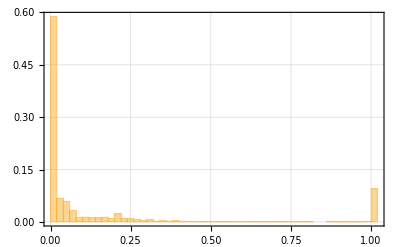

```mathematica
hist1 = Histogram[Transpose[data], 50, "Probability", PlotRange -> All, Frame->{{True,True},{True,True}}, FrameTicks->{{All,None},{All,None}}, GridLines->Automatic]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\PD_histogram.jpg",hist1]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\PD_histogram.jpg

```mathematica
R[p] = 0.12((1-e(-50p))/(1-e^(-50)))+0.24(1-(1-e^(-50p))/(1-e^(-50)))
```

```mathematica
g[p]:=  Subscript[k, 1] InverseCDF[NormalDistribution[], p]+Subscript[k, 2] InverseCDF[NormalDistribution[], 0.999]
```

```mathematica
RW[p] := 0.45(CDF[NormalDistribution[],g[p]]-p)
```

```mathematica
Sign[RW[0.99999999999]]
```

Sign[-1.+1/2 Erfc[(-6.70602 √(1/(1-0.24 (1-(1-1/e^50.)/(1-1/e^50))-(0.12 (1-1/e^50.))/(1-1/e^50)))-3.09023 √((0.24 (1-(1-1/e^50.)/(1-1/e^50))+(0.12 (1-1/e^50.))/(1-1/e^50))/(1-0.24 (1-(1-1/e^50.)/(1-1/e^50))-(0.12 (1-1/e^50.))/(1-1/e^50))))/(√2)]]

```mathematica
Sign[RW[0.00000000001]]
```

1

```mathematica
RW[1]
```

```mathematica
`
```

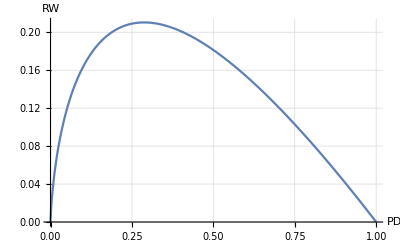

```mathematica
plot1 = Plot[{RW[p]}, {p, 0,1},GridLines->Automatic,FrameTicks->{{All,None},{All,None}}, AxesLabel->{"PD","RW"}]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\function.jpg",plot1]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\function.jpg

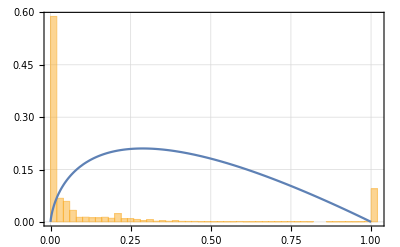

```mathematica
graph1 = Show[{hist1, plot1}]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\function_histogram.jpg",graph1]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\function_histogram.jpg

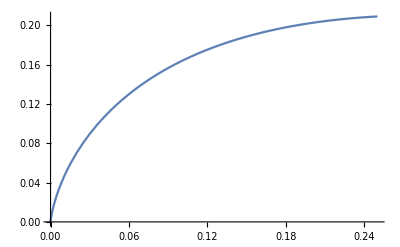

```mathematica
Plot[{RW[p]}, {p, 0,0.25}]
```

```mathematica
RW'[p]
```

```mathematica
ConditionalExpression[0.45 (-1+1.0846522890932808 ⅇ^(InverseErfc[2 p]^2-1/2 (-1.2981572260040208+1.5339299776947408 InverseErfc[2 p])^2)),0≤p≤1]
```

```mathematica
Sign[RW'[0.99999999999]]
```

-1

```mathematica
Sign[RW'[0.00000000001]]
```

```mathematica
1
```

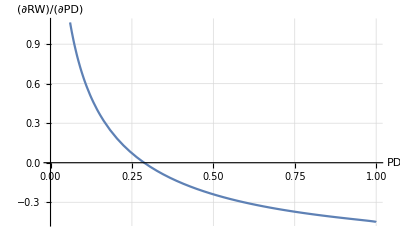

```mathematica
plot2 = Plot[{RW'[p]}, {p, 0,1}, GridLines->Automatic,FrameTicks->{{All,None},{All,None}}, AxesLabel->{"PD","(∂RW)/(∂PD)"}]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\first_derivative.jpg",plot2]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\first_derivative.jpg

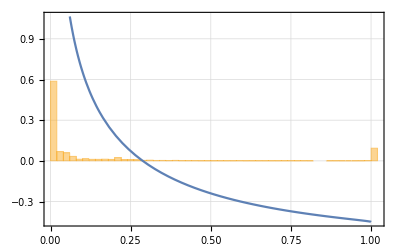

```mathematica
graph2 = Show[{hist1, plot2}]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\first_histogram.jpg",graph2]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\first_histogram.jpg

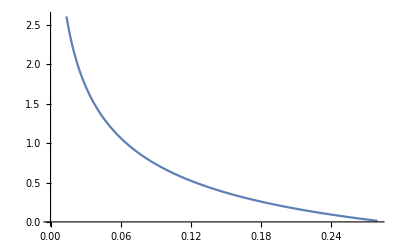

```mathematica
Plot[{RW'[p]}, {p, 0,0.28}]
```

```mathematica
RW''[p]
```

ConditionalExpression[0.488094 ⅇ^(InverseErfc[2 p]^2-1/2 (-1.29816+1.53393 InverseErfc[2 p])^2) (-2 ⅇ^(InverseErfc[2 p]^2) √π InverseErfc[2 p]+2.71882 ⅇ^(InverseErfc[2 p]^2) (-1.29816+1.53393 InverseErfc[2 p])),0≤p≤1]

```mathematica
Sign[RW''[0.99999999999]]
```

```mathematica
-1
```

```mathematica
Sign[RW''[0.00000000001]]
```

```mathematica
-1
```

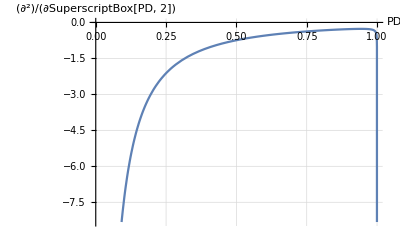

```mathematica
plot3 = Plot[{RW''[p]}, {p, 0,1}, GridLines->Automatic, FrameTicks->{{All,None},{All,None}}, AxesLabel->{"PD","∂^2/(∂SuperscriptBox[PD, 2])"}]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\second_derivative.jpg",plot3]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\second_derivative.jpg

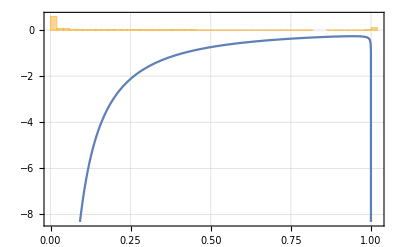

```mathematica
graph3 = Show[{hist1, plot3}]
```

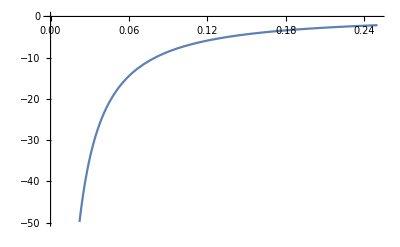

```mathematica
Plot[{RW''[p]}, {p, 0,0.25}]
```

```mathematica
RW'''[p]
```

ConditionalExpression[0.488094 ⅇ^(InverseErfc[2 p]^2-1/2 (-1.29816+1.53393 InverseErfc[2 p])^2) (-2 ⅇ^(InverseErfc[2 p]^2) √π InverseErfc[2 p]+2.71882 ⅇ^(InverseErfc[2 p]^2) (-1.29816+1.53393 InverseErfc[2 p]))^2+0.488094 ⅇ^(InverseErfc[2 p]^2-1/2 (-1.29816+1.53393 InverseErfc[2 p])^2) (-7.39198 ⅇ^(2 InverseErfc[2 p]^2)+2 ⅇ^(2 InverseErfc[2 p]^2) π+4 ⅇ^(2 InverseErfc[2 p]^2) π InverseErfc[2 p]^2-9.63797 ⅇ^(2 InverseErfc[2 p]^2) InverseErfc[2 p] (-1.29816+1.53393 InverseErfc[2 p])),0≤p≤1]

```mathematica
Sign[RW''[0.99999999999]]
```

-1

```mathematica
Sign[RW'''[0.00000000001]]
```

1

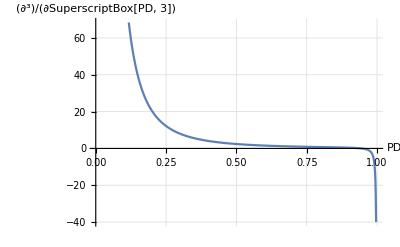

```mathematica
plot4 = Plot[{RW'''[p]}, {p, 0,1}, GridLines->Automatic, FrameTicks->{{All,None},{All,None}}, AxesLabel->{"PD","∂^3/(∂SuperscriptBox[PD, 3])"}]
```

```mathematica
Export["C:\\Users\\u1273941\\Research\\Projects\\RW_density\\Auxiliar\\Pictures\\third_derivative.jpg",plot4]
```

C:\Users\u1273941\Research\Projects\RW_density\Auxiliar\Pictures\third_derivative.jpg

```mathematica
graph4 = Show[{hist1, plot4}]
```

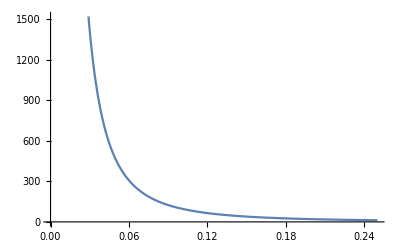

```mathematica
Plot[{RW'''[p]}, {p, 0,0.25}]
```